```mathematica
jacobi2={{4.62762+1.39202 I,0.881414 I,0},{0.881414 I,1.96443-0.215952 I,1.3132 I},{0,1.3132 I,-1.65732-1.38486 I}}
jacobi2//MatrixForm
Eigenvalues[jacobi2]
```

{{4.62762+1.39202 ⅈ,0.+0.881414 ⅈ,0},{0.+0.881414 ⅈ,1.96443-0.215952 ⅈ,0.+1.3132 ⅈ},{0,0.+1.3132 ⅈ,-1.65732-1.38486 ⅈ}}

(4.62762+1.39202 ⅈ | 0.+0.881414 ⅈ | 0
0.+0.881414 ⅈ | 1.96443-0.215952 ⅈ | 0.+1.3132 ⅈ
0 | 0.+1.3132 ⅈ | -1.65732-1.38486 ⅈ)

{4.41581+1.5204 ⅈ,-1.20172-1.56525 ⅈ,1.72064-0.163944 ⅈ}

{-1.22882-8.27398×10^-17 ⅈ,1.22882-1.24402×10^-16 ⅈ,-2.26243×10^-16+6.46095×10^-18 ⅈ}

```mathematica
exp[t_]:=MatrixExp[I*t*jacobi2];
{x1,x2,x3}=exp[t].UnitVector[3,1];
```

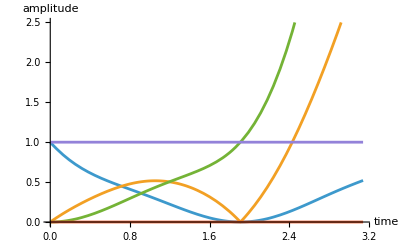

```mathematica
x=Plot[{Abs[x1],Abs[x2],Abs[x3],0 *(Abs[x1]^2-Abs[x2]^2+Abs[x3]^2),1},{t,0,1Pi},AxesLabel->{"time","amplitude"},GridLines->{{4.93},None}]
```

```mathematica
tstar=t/. FindRoot[Abs[x3]==1,{t,4.84}];

Print["Time = ",N[tstar]];
Print["Line 1 = ",N[Abs[x1]/. t->tstar]];
Print["Line 2 = ",N[Abs[x2]/. t->tstar]];
Print["Line 3 = ",N[Abs[x3]/. t->tstar]];
N[{tstar,Abs[x1]/. t->tstar,Abs[x2]/. t->tstar,Abs[x3]/. t->tstar}]
```

Time = 1.90988

Line 1 = 3.73603×10^-6

Line 2 = 3.34639×10^-6

Line 3 = 1.

{1.90988,3.73603×10^-6,3.34639×10^-6,1.}

```mathematica
Clear[a,b,c,d,e,α,β,γ,T]

H={{a+I α,I d,0},{I d,b+I β,I e},{0,I e,c+I γ}};
H//MatrixForm

psi0={1,0,0};

psi=MatrixExp[I T H].psi0;

obj=Abs[psi[[1]]]^2+Abs[psi[[2]]]^2+Abs[psi[[3]]-1]^2;

NMinimize[{obj,a-b>=0.1,b-c>=0.1,a-c>=0.2,d^2+e^2<=0.49*((a-b)^2+(a-c)^2+(b-c)^2)/2,0<d<2,0<e<2,-5<a<5,-5<b<5,-5<c<5,-3<α<3,-3<β<3,-3<γ<3,0<T<10},{a,b,c,d,e,α,β,γ,T}]
```

(a+ⅈ α | ⅈ d | 0
ⅈ d | b+ⅈ β | ⅈ e
0 | ⅈ e | c+ⅈ γ)

Max::nord: Invalid comparison with {1.99875×10^6+0. ⅈ,10.8818+0. ⅈ,9919.34+0. ⅈ,3.48868+0. ⅈ,29882.3+0. ⅈ,2.51152×10^8+0. ⅈ,2.28966+0. ⅈ,1.93964+0. ⅈ,3.39457×10^7+0. ⅈ} attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

{1.65502×10^-11,{a→4.62762,b→1.96443,c→-1.65732,d→0.881414,e→1.3132,α→1.39202,β→-0.215952,γ→-1.38486,T→1.90988}}

```mathematica
FullSimplify[Eigenvalues[{{a+ⅈ α,ⅈ d,0},{ⅈ d,b+ⅈ β,ⅈ e},{0,ⅈ e,c+ⅈ γ}}]]
```

{Root[-a b c-c d^2-a e^2-ⅈ b c α-ⅈ e^2 α-ⅈ a c β+c α β-ⅈ a b γ-ⅈ d^2 γ+b α γ+a β γ+ⅈ α β γ+(a b+a c+b c+d^2+e^2+ⅈ b α+ⅈ c α+ⅈ a β+ⅈ c β-α β+ⅈ a γ+ⅈ b γ-α γ-β γ) #1+(-a-b-c-ⅈ α-ⅈ β-ⅈ γ) #1^2+#1^3&,1],Root[-a b c-c d^2-a e^2-ⅈ b c α-ⅈ e^2 α-ⅈ a c β+c α β-ⅈ a b γ-ⅈ d^2 γ+b α γ+a β γ+ⅈ α β γ+(a b+a c+b c+d^2+e^2+ⅈ b α+ⅈ c α+ⅈ a β+ⅈ c β-α β+ⅈ a γ+ⅈ b γ-α γ-β γ) #1+(-a-b-c-ⅈ α-ⅈ β-ⅈ γ) #1^2+#1^3&,2],Root[-a b c-c d^2-a e^2-ⅈ b c α-ⅈ e^2 α-ⅈ a c β+c α β-ⅈ a b γ-ⅈ d^2 γ+b α γ+a β γ+ⅈ α β γ+(a b+a c+b c+d^2+e^2+ⅈ b α+ⅈ c α+ⅈ a β+ⅈ c β-α β+ⅈ a γ+ⅈ b γ-α γ-β γ) #1+(-a-b-c-ⅈ α-ⅈ β-ⅈ γ) #1^2+#1^3&,3]}